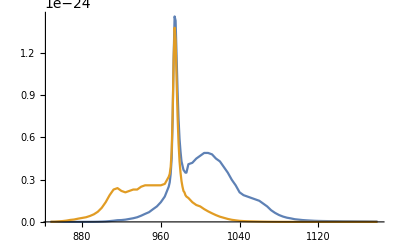

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
```

```mathematica
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

λp=960;(*нм*)
λs=1064;(*нм*)
Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

L=2;

σp12=σa[λp];
σp21=σe[λp];
σs12=σa[λs];
σs21=σe[λs];
```

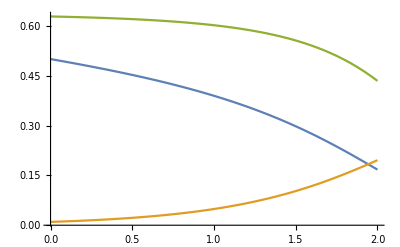

```mathematica
(*Усилитель*)
sol=NDSolve[{
0==ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN, 
Pp ρp[0]==0.5,Ps ρs[0]==0.01
},{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->-15];

Plot[Evaluate[{Pp ρp[z],Ps ρs[z],N2[z]/NN}/.sol],{z,0,L},PlotRange->All]
```

Домашнее задание 
1) Изучить Consistent Initialization, AccuracyGoal, PrecisionGoal, WorkingPrecision, tutorial/NDSolveBVP
2) Уметь вывести формулу инверсии просветления среды. Построить график зависимости инверсии просветления иттербия от длины волны.
	Из какого условия выводится формула инверсии просветления? сформулировать условие в виде формулы. Какие физические процессы отвечают за эффект просветления?
	Рассмотреть случаи, когда в активной среде каким-то образом создается инверсия произвольной величины. Уметь рассудить, что будет с инверсией и излучением, если запустить монохроматическое излучение в среду
	Аппроксимировать график функцией распределения Ферми-Дирака. Обосновать результат с точки зрения теории МакКамбера. Уметь рассказать о приближениях в теории МакКамбера.
3) Построить график зависимости мощности насыщения от длины волны для моды LP01 (считать гауссом) FWHM 7мкм для иттербиевого световода.
4) Рассмотреть усилитель, где изменением инверсии по z можно пренебречь, считать ее постоянной и заданной по всей длине x%. Аналитически решить эту задачу в Mathematica. Построить график спектра усиления такого иттербиевого волоконного усилителя. Необходимые константы и параметры задачи взять из семинара.
	Перечислить такие случаи, когда реальный прибор будет хорошо описываться такой моделью.
	Сколько существует спектральных интервалов с одинаковым по знаку коэффициентом усиления? На каких длинах волн проходит граница этих интервалов?	
	С помощью оператора Manipulate сделать инверсию динамической переменной.
	Найти зависимость длины волны с максимальным коэффициентом усиления от инверсии.	
5) Слабый сигнал - такой сигнал на входе в усилитель, влиянием которого на инверсию в усилителе можно пренебречь. Исходя из этой посылки упростить скоростные уравнения и построить график спектра коэффициента усиления слабого сигнала для усилителя, описанного в семинарской задаче.
	Решить данную задачу аналитически. Сравнить скорость аналитического решения с численным решением “в лоб” методом многократного решения скоростных уравнений. Воспользоваться оператором Timing
	Перечислить случаи, когда можно пользоваться приближением слабого сигнала дла описания работы прибора
	В иттербиевом усилителе усиливаются импульсы с энергией 0.2нДж с центральной длиной волны 1030 нм идущие с частотой 20МГц. Найти спектр на выходе из усилителя в приближении слабого сигнала для импульсов с гауссовым спектром и прямоугольным спектром, спекртральный FWHM = 18 нм. Характеристики волокна и накачки как в семинарской задаче. Посчитать FWHM спектра выходного импульса.
6) Решить задачу об усилителе для конфигурации накачки типа “двойка”, где накачка равномерно распространяется по двум волокнам 125мкм в диаметре.
	Учесть серые потери в волокне 10дБ/км